# Impact of Urban Design on Quality of Life

## Intro

Most of the population around the globe is now concentrated in cities. There are around 2 dozens urban areas with populations exceeding 10 million people, but we still fail to quantify the influence of various aspects of urban design on the quality of life.
This work is a stepping stone in that direction.

## What is quality of life?

This is a very non-trivial question and we are not going to answer it in this work. Instead we will define a very simple approximation of quality of life as average sentiment across Tweets related to that specific city.

```mathematica
EstimateSentimentWL[sentence_String] := Module[{probs, pPos, pNeu, pNeg, resultPositivness, resultCertainity},
	probs = Classify["Sentiment", sentence, "Probabilities"];
	pPos = Lookup[probs, "Positive"];
	pNeu = Lookup[probs, "Neutral"];
	pNeg = Lookup[probs, "Negative"];
	resultPositivness = (pPos + pNeu * 0.5);
	resultCertainity = Max[probs];
	{resultPositivness,resultCertainity}
];
EstimateSentiments[sentences_, func_] := Map[({#, func[#]}) &, sentences];
EstimateSentiments[sentences_] := EstimateSentiments[sentences, EstimateSentimentWL];
EstimateQualityOfLifeWSentiment[data_] := Module[{tweetsWSentiments, sentimentsWCertainity, meanPositivness, meanCertainty},
	data = data⟦All, "Text"⟧;
	tweetsWSentiments = EstimateSentiments[data];
	sentimentsWCertainity = tweetsWSentiments⟦All, 2⟧;
	meanPositivness = MeanAround[sentimentsWCertainity⟦All, 1⟧];
	meanCertainty = MeanAround[sentimentsWCertainity⟦All, 2⟧];
	{meanPositivness, meanCertainty}
];
RescaleIntoInterval[numbers_List, numberNewSmallest_, numberNewLargest_] := Map[(# * (numberNewLargest - numberNewSmallest) + numberNewSmallest) &, Rescale[numbers]];
```

## Which regions are we going to analyze?

rer

```mathematica
constantDirectory = "/Users/ashvardanian/CodeMine/WolframSummer19/Final Project/Drafts";
constantPathTweets = StringJoin[{constantDirectory, "/Tweets"}];
constantPathFeatures = StringJoin[{constantDirectory, "/Features"}];
constantPathMaps = StringJoin[{constantDirectory, "/Maps"}];
constantCityDiameterKM = 10;
constantCityGridSize = 5;
(* 
Ordered list of cities: https://www.timeout.com/things-to-do/best-cities-in-the-world 
Other lists can be found in "CitiesLists.nb".
*)
CityRowParse[cityRow_List] := { Interpreter["City"][StringJoin[cityRow⟦2⟧, ", ", cityRow⟦3⟧]], cityRow⟦1⟧ };
citiesWRanks = Map[CityRowParse, Drop[Import["/Users/ashvardanian/CodeMine/WolframSummer19/Final Project/Drafts/Inputs/CitiesMercer2019.csv"], 1]];
citiesPopular = citiesWRanks[[All, 1]];

CityName[city_] := EntityValue[city, "Name"];
CityDataPath[directory_String, city_String] := StringJoin[{directory, "/", city, ".mx"}];
CityDataPath[directory_String, city_] := CityDataPath[directory, CityName[city]];
```

Lets collect Twitter data.

```mathematica
tw = ServiceConnect["Twitter"];
ExtractTweets[city_] := Normal[tw["TweetSearch", "Query"->CityName[city]]];
ExportTweets[city_] := Export[CityDataPath[constantPathTweets, city],ExtractTweets[city]];
ImportTweets[city_] := Import[CityDataPath[constantPathTweets, city]];
```

Once we collect the data from Twitter, we want to see how the

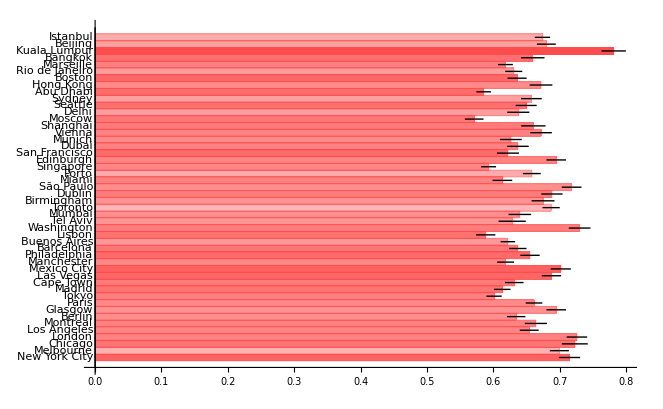

```mathematica
citiesEstimates = Map[TwEstimateQualityOfLife, citiesPopular];
citiesCertainties = RescaleIntoInterval[Map[(#["Value"]) &, citiesEstimates⟦All, 2⟧], 0.4, 1];
citiesColors = Map[RGBColor[1, 0.3, 0.3, #] &, citiesCertainties];
citiesPositivness = citiesEstimates⟦All, 1⟧;
BarChart[citiesPositivness,ChartLabels->Map[CityName, citiesPopular],BarOrigin->Left,ChartStyle->citiesColors]
```

As we can see, there is not much variance between cities, in terms of Tweets sentiment.
Lets compile multiple rankings together, assuming that they have had a more complete model for estimating the quality of life and satisfaction.

```mathematica
citiesPositivness = RescaleIntoInterval[Map[(N[1/#])&, citiesWRanks⟦All, 2⟧], 0.6, 1];
```

## Are there any correlations at all?

wew

```mathematica
ExtractMaps[city_] := Module[{cityBounds, gridLats, gridLons, cityParts, cityImages, MakeCell, ImageForCell},
	cityBounds = Normal[GeoBoundingBox[GeoPosition[city], Quantity[constantCityDiameterKM, "Kilometers"]]];
	gridLats = Subdivide[Latitude[cityBounds⟦1⟧],Latitude[cityBounds⟦2⟧], constantCityGridSize+1];
	gridLons = Subdivide[Longitude[cityBounds⟦1⟧],Longitude[cityBounds⟦2⟧], constantCityGridSize+1];
	MakeCell[i_Integer, j_Integer] := GeoRange[{gridLats⟦i⟧, gridLats⟦i+1⟧}, {gridLons⟦j⟧, gridLons⟦j+1⟧}];
	cityParts = Flatten[Table[MakeCell[i, j], {i, constantCityGridSize}, {j, constantCityGridSize}]];
	ImageForCell[coords_] := Module[{coordsAsList},
		coordsAsList = List @@ coords;
		Image[GeoGraphics[GeoRange->coordsAsList]]
	];
	cityImages = Map[ImageForCell, cityParts]
];
ExportMaps[city_] := Export[CityDataPath[constantPathMaps, city],ExtractMaps[city]];
ImportMaps[city_] := Import[CityDataPath[constantPathMaps, city]];
```

```mathematica
ExtractListFeatures[object_, props_List] := Normal[Map[({#, Normal[object[#]]}) &, props]];
ExtractCityStatsFeatures[city_] := Module[{props}, 
	props = {"Population","Latitude","Longitude","Elevation","MagneticFieldStrength"};
	ExtractListFeatures[city, props]
];
ExtractCountryStatsFeatures[city_] := Module[{props, country},
	country = city["Country"];
	props = {"Population","Latitude","Longitude",
	"Area","WaterArea","BoundaryLength",
	"ChildPopulation","ContributingFamilyWorkers","ElderlyPopulation","HIVAIDSPopulation",
	"NetIncomeFromAbroad","GovernmentDebt","GovernmentSurplus","ImportsValue","ExportsValue",
	"GiniIndex","Army"};
	ExtractListFeatures[country, props]
];
ExtractMapFeatures[city_] := Module[{},
	List[]
];
ExtractAllFeatures[city_] := Join[ExtractCityStatsFeatures[city], ExtractCountryStatsFeatures[city], ExtractMapFeatures[city]];
ExportAllFeatures[city_] := Export[CityDataPath[constantPathFeatures, city], ExtractAllFeatures[city]];
ImportAllFeatures[city_] := Import[CityDataPath[constantPathFeatures, city]];
```

```mathematica
citiesFeatures = Map[ImportAllFeatures[#]⟦All, 2⟧ &, citiesPopular];
citiesFeatures = Map[Apply[Normal, #, {1, 2}] &, citiesFeatures]; (*Transform units into raw numbers.*)
constantTrainingObjects = 80;
citiesFeaturesTrain = Take[citiesFeatures, constantTrainingObjects];
citiesFeaturesPredict = Drop[citiesFeatures, constantTrainingObjects];
citiesPositivnessTrain = Take[citiesPositivness, constantTrainingObjects];
citiesPositivnessPredict = Drop[citiesPositivness, constantTrainingObjects];

NormalizeFeatures[rowsPerSample_List] := Module[{rowsPerFeature, rowsPerFeatureNormalized},
	rowsPerFeature = Transpose[rowsPerSample];
	rowsPerFeatureNormalized = Map[(RescaleIntoInterval[Rescale[#], 0.5, 1]) &, rowsPerFeature];
	Transpose[rowsPerFeatureNormalized]
];
RunRegression[featuresValsVecs_List, predictionsVals_List, featuresNames_List] := Module[{featuresNormalized, p, pLinearLayer, pWeights},
	featuresNormalized = NormalizeFeatures[featuresValsVecs];
	p = Predict[featuresValsVecs->predictionsVals, Method->"LinearRegression"];
	pLinearLayer = p[[1,"Model", "MeanFunction"]];
	pWeights = Normal @ pLinearLayer[["Arrays"]][["Weights"]];
];
```

```mathematica
NormalizeFeatures[{{1, 30}, {2, 35}, {3, 36}}]
```

(1 | 30
2 | 35
3 | 36)

{{1,2,3},{30,35,36}}

{{0.5,0.75,1.},{0.5,0.916667,1.}}

{{0.5,0.5},{0.75,0.916667},{1.,1.}}

{{0.5,0.5},{0.75,0.916667},{1.,1.}}

```mathematica
Dimensions[citiesFeaturesTrain]
```

{80,22}

```mathematica
Take[citiesPositivnessTrain, UpTo[10]]
```

{1.,0.79798,0.73064,0.73064,0.73064,0.6633,0.65368,0.640853,0.646465,0.636364}

```mathematica
Dimensions@citiesFeaturesTrain
```

{80,22}

```mathematica
p=Predict[{1,2,3,4,5}->{.1,.2, .3, .4,.5}, Method->"LinearRegression"]
```

```mathematica
p=Predict[citiesFeaturesTrain->citiesPositivnessTrain, Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
wp=p[[1,"Model", "MeanFunction"]]
```

LinearLayer[<>]

```mathematica
Normal @ wp[["Arrays"]][["Weights"]]
```

{{1.53575×10^-6,-0.0000127028,7.26185×10^-6,-2.1447×10^-6,-0.0000234971,-1.26263×10^-6,7.44138×10^-7,0.0000187258,0.0000154906,-3.5913×10^-6,-0.0000140744,-0.0000133014,-9.73523×10^-6,-0.0000194875,6.048×10^-6,0.000017463,4.95068×10^-6,7.29797×10^-6,-0.0000119238,8.63709×10^-6,7.00634×10^-6,0.0000102419,5.39273×10^-6,-0.0000231572,-4.17449×10^-6,-6.399×10^-6,4.13765×10^-6,-7.23263×10^-7,0.0000157328,-0.0000126291,0.0000163053,-6.69346×10^-6,-8.67822×10^-6,0.0000136415,0.0000206101,-6.16139×10^-6,-7.40738×10^-6,2.0149×10^-6,4.80343×10^-6,0.0000106963,6.27587×10^-6,-0.0000171243,1.89468×10^-6,5.54001×10^-6,-0.0000108691,-0.0000102732,1.69263×10^-6,-0.0000167119,-0.000017735,0.0000169402,-0.0000143543,-0.0000128134}}

```mathematica
BarChart[%170,ChartLabels->Map[CityName, citiesPopular],BarOrigin->Left,ChartStyle->citiesColors]
```

Missing[NotPresent,{1}]

```mathematica
Keys@wp
```

Keys::invrl: The argument … is not a valid Association or a list of rules.

Keys[LinearLayer[<>]]

```mathematica
Normal[wp]
```

LinearLayer[<>]

```mathematica
Predict[citiesFeaturesTrain]
```

```mathematica
RandomSample[citiesFeaturesTrain,10]
```

{{2714719,0.441045,0.965691,20.,44.3691,9400145,0.418879,0.942478,32278.1,0.,1357.7,1.28734×10^6,3921,100499.,NotAvailable,2.7774×10^9,7.38677×10^9,5.52×10^9,2.77086×10^11,3.84044×10^11,NotAvailable,59000},{883391,0.792729,-1.32139,230.,53.3959,36624199,1.0472,-1.65806,3.8551×10^6,344080.,131093.,5.79526×10^6,24786,6.01366×10^6,73000.,-1.78156×10^10,8.14597×10^11,7.×10^9,5.50261×10^11,5.11412×10^11,0.34,40300},{486290,0.589274,-1.47345,1050.,48.3924,324459463,0.663225,-1.69297,3.71871×10^6,181274.,19857.8,6.14855×10^7,77608,4.85708×10^7,1.2×10^6,243667000000,1.85262×10^13,-4.55×10^11,2928596000000,2350175000000,0.415,512000},{693972,0.679005,-1.3442,20.,50.4545,324459463,0.663225,-1.69297,3.71871×10^6,181274.,19857.8,6.14855×10^7,77608,4.85708×10^7,1.2×10^6,243667000000,1.85262×10^13,-4.55×10^11,2928596000000,2350175000000,0.415,512000},{673104,0.739724,-1.45041,600.,52.8684,324459463,0.663225,-1.69297,3.71871×10^6,181274.,19857.8,6.14855×10^7,77608,4.85708×10^7,1.2×10^6,243667000000,1.85262×10^13,-4.55×10^11,2928596000000,2350175000000,0.415,512000},{281000,0.952659,-0.103556,33.,49.6628,66181585,0.942478,-0.0349066,94058.3,648.652,7946.72,1.15645×10^7,116252,1.20447×10^7,77000.,-4.22096×10^10,3.07934×10^12,-6.96×10^10,8.25573×10^11,7.94771×10^11,0.332,112130},{639407,0.894307,0.118508,140.,49.1233,82114224,0.890118,0.15708,137847.,3223.95,3786.64,1.08208×10^7,147901,1.75831×10^7,53000.,7.76901×10^10,1.69761×10^12,-1.13×10^11,1.45832×10^12,1.73755×10^12,0.317,115730},{601448,0.971799,0.219388,46.,50.5001,5733551,0.977384,0.174533,16638.7,254.827,4586.96,951041.,10983,1.11361×10^6,4800.,6.77521×10^9,1.2822×10^11,9.×10^9,1.56513×10^11,1.79922×10^11,0.282,10500},{7234800,0.388929,1.99229,290.,45.5401,7364883,0.388336,1.99258,426.257,19.3051,474.106,823711.,10459,1.15827×10^6,2600.,1.42091×10^10,NotAvailable,-9.9×10^8,6.38819×10^11,6.41927×10^11,0.4344,NotAvailable},{724745,0.831135,-2.13543,180.,52.843,324459463,0.663225,-1.69297,3.71871×10^6,181274.,19857.8,6.14855×10^7,77608,4.85708×10^7,1.2×10^6,243667000000,1.85262×10^13,-4.55×10^11,2928596000000,2350175000000,0.415,512000}}

```mathematica
NetTrain[NetChain[{LinearLayer[{}],ElementwiseLayer[LogisticSigmoid]},"Input"->22],citiesFeaturesTrain-> citiesFeaturesPredict,LossFunction->MeanSquaredLossLayer[]]
```

NetTrain::invinlen: Inconsistent numbers of examples provided to ports: lengths were <|Input→80,Output→20|>.

$Failed

```mathematica
p=LinearModelFit[{citiesFeaturesTrain, citiesPositivnessTrain}];
```

LinearModelFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

```mathematica
p[citiesFeaturesPredict] - citiesPositivnessPredict
```

{0.0212998,0.0213592,0.0214194,0.0214759,0.0215311,0.0215901,0.0215906,0.0216779,0.021747,0.021799,0.0218411,0.0218944,0.0219378,0.0219848,0.0220159,0.022066,0.0221178,0.022166,0.0221627,0.0222464}

## Are there correlations between cities topology and quality of life?

wewe

## Are there correlations between known features and quality of life?

wewe